# Constrained Interpolation Methods

## by Manuel Diaz, NTU, 2015.08.10.

```mathematica
Quit[];
```

## Proposed Interpolation Functions

```mathematica
f0[ξ_]:=a+b ξ+c ξ^2

f1[ξ_]:=a + b ξ+c ξ^2+d ξ^3

f2[ξ_]:=(a+b ξ+c ξ^2)/(1+ e ξ)

f3[ξ_]:=-c/a Δx Log[ξ-Δx/2(2/a-1)]+-d/b Δx Log[ξ-Δx/2(2/b-1)]
```

### Just Testing

```mathematica
f0[-Δx/2]
f0[+Δx/2]
f1[-Δx/2]
f1[+Δx/2]
f2[-Δx/2]
f2[+Δx/2]
f3[-Δx/2]//Simplify
f3[+Δx/2]//Simplify
```

a-(b Δx)/2+(c Δx^2)/4

a+(b Δx)/2+(c Δx^2)/4

a-(b Δx)/2+(c Δx^2)/4-(d Δx^3)/8

a+(b Δx)/2+(c Δx^2)/4+(d Δx^3)/8

(a-(b Δx)/2+(c Δx^2)/4)/(1-(e Δx)/2)

(a+(b Δx)/2+(c Δx^2)/4)/(1+(e Δx)/2)

-(Δx (b c Log[-Δx/a]+a d Log[-Δx/b]))/(a b)

-(Δx (b c Log[((-1+a) Δx)/a]+a d Log[((-1+b) Δx)/b]))/(a b)

```mathematica
f0'[-Δx/2]
f0'[+Δx/2]
f1'[-Δx/2]
f1'[+Δx/2]
f2'[-Δx/2]/.(a-(b Δx)/2+(c Δx^2)/4 )-> Subscript[f, i-1/2] (1-(d Δx)/2)
f2'[+Δx/2]/.(a+(b Δx)/2+(c Δx^2)/4 )-> Subscript[f, i+1/2] (1+(d Δx)/2)
f3'[-Δx/2]//Simplify
f3'[+Δx/2]//Simplify
```

b-c Δx

b+c Δx

b-c Δx+(3 d Δx^2)/4

b+c Δx+(3 d Δx^2)/4

(b-c Δx)/(1-(e Δx)/2)-(e (1-(d Δx)/2) f_(-1/2+i))/(1-(e Δx)/2)^2

(b+c Δx)/(1+(e Δx)/2)-(e (1+(d Δx)/2) f_(1/2+i))/(1+(e Δx)/2)^2

c+d

(c-b c+d-a d)/((-1+a) (-1+b))

## Interpolating Polynomial f0[x]

### constrains

```mathematica
f0'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx
f0'[Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx
```

b-c Δx==(-f_(-1+i)+f_i)/Δx

b+c Δx==(-f_i+f_(1+i))/Δx

```mathematica
Simplify[1/Δx∫_(-Δx/2)^(Δx/2) f0[ξ]ⅆξ ]== Subscript[f, i]
```

a+(c Δx^2)/12==f_i

### solving as a system of equations

```mathematica
coefs= Solve[f0'[Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx && f0'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx &&+1/Δx∫_(-Δx/2)^(Δx/2) f0[ξ]ⅆξ == Subscript[f, i],{a,b,c}]
```

{{a→1/24 (-f_(-1+i)+26 f_i-f_(1+i)),b→-(f_(-1+i)-f_(1+i))/(2 Δx),c→-(-f_(-1+i)+2 f_i-f_(1+i))/(2 Δx^2)}}

```mathematica
f0[-Δx/2]/. coefs //Expand
f0[Δx/2] /. coefs //Expand
```

{(f_(-1+i))/3+(5 f_i)/6-(f_(1+i))/6}

{-1/6 f_(-1+i)+(5 f_i)/6+(f_(1+i))/3}

```mathematica
coefs= Solve[f0'[Δx/2]==Subscript[d, i+1/2]/Δx && f0'[-Δx/2]==Subscript[d, i-1/2]/Δx &&+1/Δx∫_(-Δx/2)^(Δx/2) f0[ξ]ⅆξ == Subscript[f, i],{a,b,c}]
```

{{a→1/24 (d_(-1/2+i)-d_(1/2+i)+24 f_i),b→-(-d_(-1/2+i)-d_(1/2+i))/(2 Δx),c→-(d_(-1/2+i)-d_(1/2+i))/(2 Δx^2)}}

## Interpolating Polynomial f1[x]

### constrains

```mathematica
f1'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx
f1'[Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx
```

b-c Δx+(3 d Δx^2)/4==(-f_(-1+i)+f_i)/Δx

b+c Δx+(3 d Δx^2)/4==(-f_i+f_(1+i))/Δx

```mathematica
Simplify[1/Δx∫_(-Δx/2)^(Δx/2) f1[ξ]ⅆξ ]== Subscript[f, i]
```

a+(c Δx^2)/12==f_i

### solving as a system of equations

```mathematica
coefs= Solve[f1'[Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx && f1'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx &&+1/Δx∫_(-Δx/2)^(Δx/2) f1[ξ]ⅆξ == Subscript[f, i],{a,c,d}]
```

{{a→1/24 (-f_(-1+i)+26 f_i-f_(1+i)),c→-(-f_(-1+i)+2 f_i-f_(1+i))/(2 Δx^2),d→-(2 (2 b Δx+f_(-1+i)-f_(1+i)))/(3 Δx^3)}}

```mathematica
f1[-Δx/2]/. coefs //Expand
f1[Δx/2] /. coefs //Expand
```

{-(b Δx)/3+(f_(-1+i))/6+(5 f_i)/6}

{(b Δx)/3+(5 f_i)/6+(f_(1+i))/6}

What is b? 
To find out we will assuming and extra constrain:

```mathematica
bcoef = Solve[f1'[0]==(Subscript[f, i+1]-Subscript[f, i-1])/(2Δx),b]
```

{{b→(-f_(-1+i)+f_(1+i))/(2 Δx)}}

```mathematica
f1[-Δx/2]/. coefs /.bcoef//Expand
f1[Δx/2] /. coefs /.bcoef//Expand
```

{{(f_(-1+i))/3+(5 f_i)/6-(f_(1+i))/6}}

{{-1/6 f_(-1+i)+(5 f_i)/6+(f_(1+i))/3}}

NOTE: this is exactly the result from using polynomial f0[x]!

```mathematica
Clear[d];
```

```mathematica
coefs= Solve[f1'[Δx/2]==Subscript[δ, i+1/2]/Δx && f1'[-Δx/2]==Subscript[δ, i-1/2]/Δx &&+1/Δx∫_(-Δx/2)^(Δx/2) f1[ξ]ⅆξ == Subscript[f, i],{a,c,d}]
```

{{a→1/24 (24 f_i+δ_(-1/2+i)-δ_(1/2+i)),c→-(δ_(-1/2+i)-δ_(1/2+i))/(2 Δx^2),d→-(2 (2 b Δx-δ_(-1/2+i)-δ_(1/2+i)))/(3 Δx^3)}}

Therefore, it is obvious that we can choose ‘b’ as a free parameter to control the slope of the approximation!

## Non-polynomial Interpolation function f2[x]

### constrains

```mathematica
f2'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx
f2'[+Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx
```

(b-c Δx)/(1-(e Δx)/2)-(e (a-(b Δx)/2+(c Δx^2)/4))/(1-(e Δx)/2)^2==(-f_(-1+i)+f_i)/Δx

(b+c Δx)/(1+(e Δx)/2)-(e (a+(b Δx)/2+(c Δx^2)/4))/(1+(e Δx)/2)^2==(-f_i+f_(1+i))/Δx

```mathematica
Simplify[1/Δx∫_(-Δx/2)^(Δx/2) f2[ξ]ⅆξ ]== Subscript[f, i]
```

ConditionalExpression[(e (-c+b e) Δx+2 (c+e (-b+a e)) ArcTanh[(e Δx)/2])/(e^3 Δx)==f_i,Re[1/(e Δx)]>1/2||Re[1/(e Δx)]<-1/2||1/(e Δx)∉Reals]

### Solve system

```mathematica
coefs= Solve[f2'[Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx && f2'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx &&+
1/(e^3 Δx)(e (-c+b e) Δx+2 (c+e (-b+a e)) ArcTanh[(e Δx)/2])==Subscript[f, i],{a,b,c}]//Simplify
```

{{a→1/(32 e^3 Δx^3)((-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(-1+i)+(-2 e Δx (16-24 e^2 Δx^2+e^4 Δx^4)+4 (-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(1+i)),b→-1/(16 e^2 Δx^3)((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(-1+i)-2 (-8 e Δx+6 e^3 Δx^3+(-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(1+i)),c→1/(8 Δx^2)((-2+e Δx)^2 f_(-1+i)-2 (4+e^2 Δx^2) f_i+(2+e Δx)^2 f_(1+i))}}

for example notice that

```mathematica
((-2+e Δx)^2 Subscript[f, -1+i]-2 (4+e^2 Δx^2) Subscript[f, i]+(2+e Δx)^2 Subscript[f, 1+i])/(8 Δx^2)/.e->0 //Simplify
```

(f_(-1+i)-2 f_i+f_(1+i))/(2 Δx^2)

```mathematica
f2[-Δx/2]/. coefs 
f2[+Δx/2] /. coefs
```

{1/(1-(e Δx)/2)(1/32 ((-2+e Δx)^2 f_(-1+i)-2 (4+e^2 Δx^2) f_i+(2+e Δx)^2 f_(1+i))+1/(32 e^3 Δx^3)((-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(-1+i)+(-2 e Δx (16-24 e^2 Δx^2+e^4 Δx^4)+4 (-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(1+i))+1/(32 e^2 Δx^2)((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(-1+i)-2 (-8 e Δx+6 e^3 Δx^3+(-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(1+i)))}

{1/(1+(e Δx)/2)(1/32 ((-2+e Δx)^2 f_(-1+i)-2 (4+e^2 Δx^2) f_i+(2+e Δx)^2 f_(1+i))+1/(32 e^3 Δx^3)((-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(-1+i)+(-2 e Δx (16-24 e^2 Δx^2+e^4 Δx^4)+4 (-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) f_(1+i))-1/(32 e^2 Δx^2)((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(-1+i)-2 (-8 e Δx+6 e^3 Δx^3+(-4+e^2 Δx^2)^2 ArcTanh[(e Δx)/2]) f_i+(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) f_(1+i)))}

which is consisten with previous results. Re-compute with d-slopes variables:

```mathematica
coefs= Solve[f2'[Δx/2]==Subscript[d, i+1/2]/Δx && f2'[-Δx/2]==Subscript[d, i-1/2]/Δx &&+
(e (-c+b e) Δx+2 (c+e (-b+a e)) ArcTanh[(e Δx)/2])/(e^3 Δx)==Subscript[f, i],{a,b,c}]//Simplify
```

{{a→(-(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(-1/2+i)+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(1/2+i)+32 e^3 Δx^3 f_i)/(32 e^3 Δx^3),b→((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(-1/2+i)-(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(1/2+i)+16 e^3 Δx^3 f_i)/(16 e^2 Δx^3),c→(-(-2+e Δx)^2 d_(-1/2+i)+(2+e Δx)^2 d_(1/2+i))/(8 Δx^2)}}

```mathematica
f2[-Δx/2]/. coefs 
f2[+Δx/2] /. coefs
```

{1/(1-(e Δx)/2)(1/32 (-(-2+e Δx)^2 d_(-1/2+i)+(2+e Δx)^2 d_(1/2+i))-((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(-1/2+i)-(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(1/2+i)+16 e^3 Δx^3 f_i)/(32 e^2 Δx^2)+(-(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(-1/2+i)+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(1/2+i)+32 e^3 Δx^3 f_i)/(32 e^3 Δx^3))}

{1/(1+(e Δx)/2)(1/32 (-(-2+e Δx)^2 d_(-1/2+i)+(2+e Δx)^2 d_(1/2+i))+((-2+e Δx)^2 (-2 e Δx+(2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(-1/2+i)-(2+e Δx)^2 (-2 e Δx+(-2+e Δx)^2 ArcTanh[(e Δx)/2]) d_(1/2+i)+16 e^3 Δx^3 f_i)/(32 e^2 Δx^2)+(-(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(-1/2+i)+(-4+e^2 Δx^2)^2 (e Δx-2 ArcTanh[(e Δx)/2]) d_(1/2+i)+32 e^3 Δx^3 f_i)/(32 e^3 Δx^3))}

How to define variable e?

What’s the derivative of ArcTanh[x]?

```mathematica
ArcTanh'[(e Δx)/2]//Simplify
```

4/(4-e^2 Δx^2)

can we approximate Tanh^-1[x] some how?

```mathematica
Series[ArcTanh[x],{x,0,24}]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19+x^21/21+x^23/23+O[x]^25

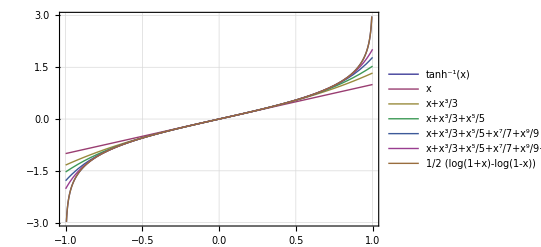

```mathematica
Plot[{ArcTanh[x],x,x+x^3/3,x+x^3/3+x^5/5,x+x^3/3+x^5/5+x^7/7+x^9/9,x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15,1/2(Log[1+x]-Log[1-x]) },{x,-1,1},PlotLegends->"Expressions",PlotStyle->Thick,Frame->True,GridLines->Automatic]
```

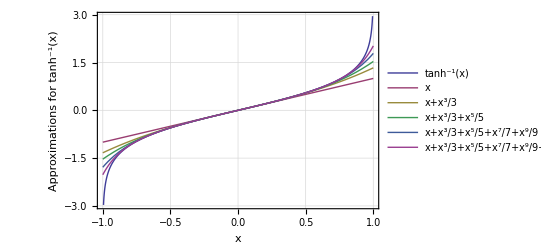

```mathematica
Plot[{ArcTanh[x],x,x+x^3/3,x+x^3/3+x^5/5,x+x^3/3+x^5/5+x^7/7+x^9/9,x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15 },{x,-1,1},PlotLegends->"Expressions",PlotStyle->Thick,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],AxesLabel->{x,"Approximations for tanh^-1(x)"}]
```

```mathematica
Export["ArcTanh.pdf",%]
```

ArcTanh.pdf

Yes! It can be approximated very well, and as long as Δx → 0. ( Which is always a desirable feature. ;D )

## Non-polynomial Interpolation function f3[x] (incomplete)

### constrains

```mathematica
f3'[-Δx/2]==(Subscript[f, i]-Subscript[f, i-1])/Δx//Simplify
f3'[+Δx/2]==(Subscript[f, i+1]-Subscript[f, i])/Δx//Simplify
```

c+d==(-f_(-1+i)+f_i)/Δx

(c-b c+d-a d)/((-1+a) (-1+b))==(-f_i+f_(1+i))/Δx

solving for c and d

```mathematica
cnd=Solve[{f3'[-Δx/2]==δ1&&f3'[+Δx/2]==δ2},{c,d}]//Simplify
```

{{c→((-1+a) (δ1+(-1+b) δ2))/(a-b),d→-((-1+b) (δ1+(-1+a) δ2))/(a-b)}}

yes, but in the paper we found that

```mathematica
d==-((-1+b) (δ1+(-1+a) δ2))/(a-b)/.Solve[c==((-1+a) (δ1+(-1+b) δ2))/(a-b),δ2]//Simplify
```

{c+d==δ1}

symmetry condition δ1 = -δ2 when r’[0] = 0.

```mathematica
f3'[0]==0/.cnd/.δ1->-δ2//Simplify
```

{((a (-1+b)-b) δ2)/((-2+a) (-2+b))==0}

```mathematica
Solve[f3'[0]==0,{b}]/.δ1->-δ2//Simplify
```

{{b→(2 c+2 d-a d)/c}}

therefore

```mathematica
b==a/(a-1);
```

lets examing f3[x] with detail:

```mathematica
f3[ξ]
```

-(c Δx Log[-1/2 (-1+2/a) Δx+ξ])/a-(d Δx Log[-1/2 (-1+2/b) Δx+ξ])/b

```mathematica
Assuming[{Re[a]<1,Re[Δx]>0},1/Δx∫_(-Δx/2)^(Δx/2) (c Δx Log[-1/2 (-1+2/a) Δx+ξ])/a ⅆξ ]
```

(c Δx (2 a ArcTanh[1-a]-2 Log[2-a]-(-2+a) Log[-2+a]-2 Log[-1+a]+a (-2+Log[-1/a]+2 Log[(-1+a) Δx])))/(2 a^2)

```mathematica
Assuming[{Re[b]<1,Re[Δx]>0},1/Δx∫_(-Δx/2)^(Δx/2) (d Δx Log[-1/2 (-1+2/b) Δx+ξ])/b ⅆξ ]
```

(d Δx (2 b ArcTanh[1-b]-2 Log[2-b]-(-2+b) Log[-2+b]-2 Log[-1+b]+b (-2+Log[-1/b]+2 Log[(-1+b) Δx])))/(2 b^2)

recall that for any given ‘x’ value:

```mathematica
{1/2(Log[1+x]-Log[1-x])== ArcTanh[x]}/.x-> 0.656
```

{True}

## MCV3

### constrains

```mathematica
f1[-1]==Subscript[f, L]
f1[1]==Subscript[f, R]
```

a-b+c-d==f_L

a+b+c+d==f_R

```mathematica
f1'[-1]==Subscript[f', L]
f1'[1]==Subscript[f', R]
```

b-2 c+3 d==f'_L

b+2 c+3 d==f'_R

### solving as a system of equations

```mathematica
coefs= Solve[f1[-1]==Subscript[f, L] && f1[1]==Subscript[f, R]&&f1'[-1]==Subscript[f', L]&& f1'[1]==Subscript[f', R],{a,b,c,d}]//Simplify
```

{{a→1/4 (2 f_L+2 f_R+f'_L-f'_R),b→1/4 (-3 f_L+3 f_R-f'_L-f'_R),c→1/4 (-f'_L+f'_R),d→1/4 (f_L-f_R+f'_L+f'_R)}}

```mathematica
f1[ξ]/. coefs
```

{1/4 ξ (-3 f_L+3 f_R-f'_L-f'_R)+1/4 (2 f_L+2 f_R+f'_L-f'_R)+1/4 ξ^2 (-f'_L+f'_R)+1/4 ξ^3 (f_L-f_R+f'_L+f'_R)}

```mathematica
f1'[ξ]/. coefs
```

{1/4 (-3 f_L+3 f_R-f'_L-f'_R)+1/2 ξ (-f'_L+f'_R)+3/4 ξ^2 (f_L-f_R+f'_L+f'_R)}

```mathematica
f1'[-1]/. coefs //Simplify
f1'[ 0 ]/. coefs //Simplify
f1'[+1] /. coefs //Simplify
```

{f'_L}

{1/4 (-3 f_L+3 f_R-f'_L-f'_R)}

{f'_R}

## MCV3-UPCC

primary lagrange interpolation at solutions points ξ = {-1,0,1}:

```mathematica
p[ξ_]:=ξ/2(ξ-1)Subscript[f, L]-(ξ+1)(ξ-1)Subscript[f, C]+ξ/2(ξ+1)Subscript[f, R];
```

```mathematica
p'[0]
```

-f_L/2+f_R/2

```mathematica
p''[0]
```

-2 f_C+f_L+f_R

now we consider a new approximation function

```mathematica
f4[ξ_]:=a + b ξ+c ξ^2+d ξ^3+e ξ^4
```

### constrains

```mathematica
f4[-1]==Subscript[P, L]
f4[0]==Subscript[f, C]
f4[1]==Subscript[P, R]
```

a-b+c-d+e==P_L

a==f_C

a+b+c+d+e==P_R

```mathematica
f4'[0]==p'[0]
f4''[0]==p''[0]
```

b==-f_L/2+f_R/2

2 c==-2 f_C+f_L+f_R

### solving as a system of equations

```mathematica
coefs= Solve[f4[-1]==Subscript[P, L]&& f4[0]==Subscript[f, C]&&f4[1]==Subscript[P, R]&&f4'[0]==p'[0]&&f4''[0]==p''[0],{a,b,c,d,e}]//Simplify
```

{{a→f_C,b→1/2 (-f_L+f_R),c→1/2 (-2 f_C+f_L+f_R),d→1/2 (f_L-f_R-P_L+P_R),e→1/2 (-f_L-f_R+P_L+P_R)}}

```mathematica
f4[ξ]/. coefs
```

{f_C+1/2 ξ (-f_L+f_R)+1/2 ξ^2 (-2 f_C+f_L+f_R)+1/2 ξ^3 (f_L-f_R-P_L+P_R)+1/2 ξ^4 (-f_L-f_R+P_L+P_R)}

```mathematica
f4'[ξ]/. coefs
```

{1/2 (-f_L+f_R)+ξ (-2 f_C+f_L+f_R)+3/2 ξ^2 (f_L-f_R-P_L+P_R)+2 ξ^3 (-f_L-f_R+P_L+P_R)}

```mathematica
f4'[-1]/. coefs //Expand
f4'[ 0 ]/. coefs //Expand
f4'[+1]/. coefs //Expand
```

{2 f_C+2 f_L-(7 P_L)/2-P_R/2}

{-f_L/2+f_R/2}

{-2 f_C-2 f_R+P_L/2+(7 P_R)/2}

## MCV3-CPCC

primary lagrange interpolation at solutions points ξ = {-sqrt(3)/2,0,sqrt(3)/2}:

```mathematica
ξ1=-(√3)/2;ξ2=0;ξ3=(√3)/2;
```

```mathematica
p[ξ_]:=((ξ-ξ2)(ξ-ξ3))/((ξ1-ξ2)(ξ1-ξ3))Subscript[f, L]+((ξ-ξ1)(ξ-ξ3))/((ξ2-ξ1)(ξ2-ξ3))Subscript[f, C]+((ξ-ξ1)(ξ-ξ2))/((ξ3-ξ1)(ξ3-ξ2))Subscript[f, R];
```

```mathematica
p'[0]
```

-f_L/(√3)+f_R/(√3)

```mathematica
p''[0]
```

-(8 f_C)/3+(4 f_L)/3+(4 f_R)/3

now we consider a new approximation function

```mathematica
f4[ξ_]:=a + b ξ+c ξ^2+d ξ^3+e ξ^4
```

### constrains

```mathematica
f4[-1]==Subscript[P, L]
f4[0]==Subscript[f, C]
f4[1]==Subscript[P, R]
```

a-b+c-d+e==P_L

a==f_C

a+b+c+d+e==P_R

```mathematica
f4'[0]==p'[0]
f4''[0]==p''[0]
```

b==-f_L/(√3)+f_R/(√3)

2 c==-(8 f_C)/3+(4 f_L)/3+(4 f_R)/3

### solving as a system of equations

```mathematica
coefs= Solve[f4[-1]==Subscript[P, L]&& f4[0]==Subscript[f, C]&&f4[1]==Subscript[P, R]&&f4'[0]==p'[0]&&f4''[0]==p''[0],{a,b,c,d,e}]//Simplify
```

{{a→f_C,b→(-f_L+f_R)/(√3),c→-2/3 (2 f_C-f_L-f_R),d→1/6 (2 √3 f_L-2 √3 f_R-3 P_L+3 P_R),e→1/6 (2 f_C-4 f_L-4 f_R+3 P_L+3 P_R)}}

```mathematica
f4[ξ]/. coefs
```

{f_C-2/3 ξ^2 (2 f_C-f_L-f_R)+(ξ (-f_L+f_R))/(√3)+1/6 ξ^3 (2 √3 f_L-2 √3 f_R-3 P_L+3 P_R)+1/6 ξ^4 (2 f_C-4 f_L-4 f_R+3 P_L+3 P_R)}

```mathematica
f4'[ξ]/. coefs
```

{-4/3 ξ (2 f_C-f_L-f_R)+(-f_L+f_R)/(√3)+1/2 ξ^2 (2 √3 f_L-2 √3 f_R-3 P_L+3 P_R)+2/3 ξ^3 (2 f_C-4 f_L-4 f_R+3 P_L+3 P_R)}

```mathematica
f4'[-√3/2]/. coefs //Expand
f4'[ 0 ]/. coefs //Expand
f4'[ √3/2 ]/. coefs //Expand
```

{(5 f_C)/(2 √3)+(3 √3 f_L)/4-f_R/(4 √3)-(9 P_L)/8-(3 √3 P_L)/4+(9 P_R)/8-(3 √3 P_R)/4}

{-f_L/(√3)+f_R/(√3)}

{-(5 f_C)/(2 √3)+f_L/(4 √3)-(3 √3 f_R)/4-(9 P_L)/8+(3 √3 P_L)/4+(9 P_R)/8+(3 √3 P_R)/4}

## CIP-CSL3

Notice that the information to be evolved are the cell boundary values!

### constrains

```mathematica
f1[-Δx/2]==Subscript[f, i-1/2]
f1[Δx/2]==Subscript[f, i+1/2]
```

a-(b Δx)/2+(c Δx^2)/4-(d Δx^3)/8==f_(-1/2+i)

a+(b Δx)/2+(c Δx^2)/4+(d Δx^3)/8==f_(1/2+i)

```mathematica
Simplify[1/Δx∫_(-Δx/2)^(Δx/2) f1[ξ]ⅆξ ]== Subscript[f, i]
```

a+(c Δx^2)/12==f_i

```mathematica
f1'[0] == Subscript[dd, i]
```

b==dd_i

### solving as a system of equations

```mathematica
coefs= Solve[f1[Δx/2]==Subscript[f, i+1/2] && f1[-Δx/2]==Subscript[f, i-1/2] &&1/Δx∫_(-Δx/2)^(Δx/2) f1[ξ]ⅆξ == Subscript[f, i]&&f1'[0] == Subscript[dd, i],{a,b,c,d}]//Expand
```

{{a→-1/4 f_(-1/2+i)+(3 f_i)/2-1/4 f_(1/2+i),b→dd_i,c→(3 f_(-1/2+i))/Δx^2-(6 f_i)/Δx^2+(3 f_(1/2+i))/Δx^2,d→-(4 dd_i)/Δx^2-(4 f_(-1/2+i))/Δx^3+(4 f_(1/2+i))/Δx^3}}

```mathematica
f1[x-Subscript[x, i-1/2]]/. coefs (*x \in [Subscript[x, i-1/2],Subscript[x, i+1/2]] *)
```

{-1/4 f_(-1/2+i)+(3 f_i)/2-1/4 f_(1/2+i)+dd_i (x-x_(-1/2+i))+((3 f_(-1/2+i))/Δx^2-(6 f_i)/Δx^2+(3 f_(1/2+i))/Δx^2) (x-x_(-1/2+i))^2+(-(4 dd_i)/Δx^2-(4 f_(-1/2+i))/Δx^3+(4 f_(1/2+i))/Δx^3) (x-x_(-1/2+i))^3}

is f_i the cell center value?

```mathematica
a+(c Δx^2)/12/. coefs//Simplify
```

{f_i}

yes!

## CIP-CSL3 (Yabe (2001) paper version)

Notice that the information to be evolved are the cell boundary values!

### Left side constrains

```mathematica
f1[-Δx]==Subscript[f, i-1]
f1[0]==Subscript[f, i]
```

a-b Δx+c Δx^2-d Δx^3==f_(-1+i)

a==f_i

```mathematica
Simplify[∫_-Δx^0 f1[ξ]ⅆξ ]== Subscript[ρ, i-1/2]
```

1/12 Δx (12 a+Δx (-6 b+Δx (4 c-3 d Δx)))==ρ_(-1/2+i)

```mathematica
f1'[-Δx/2] == Subscript[s, i-1/2]
```

b-c Δx+(3 d Δx^2)/4==s_(-1/2+i)

#### Solving as a system of equations

```mathematica
coefs= Solve[f1[ 0 ]==Subscript[f, i] && f1[-Δx]==Subscript[f, i-1] &&∫_-Δx^0 f1[ξ]ⅆξ  ==  Subscript[ρ, i-1/2]&&f1'[-Δx/2] == Subscript[s, i-1/2],{a,b,c,d}]//Expand
```

{{a→f_i,b→(6 f_i)/Δx-2 s_(-1/2+i)-(6 ρ_(-1/2+i))/Δx^2,c→-(3 f_(-1+i))/Δx^2+(9 f_i)/Δx^2-(6 s_(-1/2+i))/Δx-(6 ρ_(-1/2+i))/Δx^3,d→-(4 f_(-1+i))/Δx^3+(4 f_i)/Δx^3-(4 s_(-1/2+i))/Δx^2}}

```mathematica
f1[x-Subscript[x, i]]/. coefs (* x \in [Subscript[x, i-1],Subscript[x, i]] *)
```

{f_i+(-(4 f_(-1+i))/Δx^3+(4 f_i)/Δx^3-(4 s_(-1/2+i))/Δx^2) (x-x_i)^3+(x-x_i)^2 (-(3 f_(-1+i))/Δx^2+(9 f_i)/Δx^2-(6 s_(-1/2+i))/Δx-(6 ρ_(-1/2+i))/Δx^3)+(x-x_i) ((6 f_i)/Δx-2 s_(-1/2+i)-(6 ρ_(-1/2+i))/Δx^2)}

evaluating the time integral of u * f1( x_i-ut ) yields

```mathematica
∫_-Δt^0 u f1[-u t] ⅆt
```

a u Δt+1/2 b u^2 Δt^2+1/3 c u^3 Δt^3+1/4 d u^4 Δt^4

NOTE: u Δt indicates the direction of the advecting wave.

d_(1±1/2) are here free parameters. Note that we can define it by using the resulting interpolation functions evaluating at Δx/2 and/or -Δx/2. e.g. :

```mathematica
f1[-Δx/2]/. coefs //Expand
```

{-1/4 f_(-1+i)-f_i/4+(3 ρ_(-1/2+i))/(2 Δx)}

this is in agreement with equation (23) in Yabe [2001].

### Right side constrains

```mathematica
f1[ 0 ]==Subscript[f, i]
f1[Δx]==Subscript[f, i+1]
```

a==f_i

a+b Δx+c Δx^2+d Δx^3==f_(1+i)

```mathematica
Simplify[∫_0^Δx f1[ξ]ⅆξ ]== Subscript[ρ, i+1/2]
```

1/12 Δx (12 a+Δx (6 b+Δx (4 c+3 d Δx)))==ρ_(1/2+i)

```mathematica
f1'[Δx/2] == Subscript[s, i+1/2]
```

b+c Δx+(3 d Δx^2)/4==s_(1/2+i)

#### Solving as a system of equations

```mathematica
coefs= Solve[f1[ 0 ]==Subscript[f, i] && f1[Δx]==Subscript[f, i+1] &&∫_0^Δx f1[ξ]ⅆξ  ==  Subscript[ρ, i+1/2]&&f1'[Δx/2] == Subscript[s, i+1/2],{a,b,c,d}]//Expand
```

{{a→f_i,b→-(6 f_i)/Δx-2 s_(1/2+i)+(6 ρ_(1/2+i))/Δx^2,c→(9 f_i)/Δx^2-(3 f_(1+i))/Δx^2+(6 s_(1/2+i))/Δx-(6 ρ_(1/2+i))/Δx^3,d→-(4 f_i)/Δx^3+(4 f_(1+i))/Δx^3-(4 s_(1/2+i))/Δx^2}}

```mathematica
f1[x-Subscript[x, i-1]]/. coefs (* x \in [Subscript[x, i],Subscript[x, i+1]] *)
```

{f_i+(-(4 f_i)/Δx^3+(4 f_(1+i))/Δx^3-(4 s_(1/2+i))/Δx^2) (x-x_(-1+i))^3+(x-x_(-1+i))^2 ((9 f_i)/Δx^2-(3 f_(1+i))/Δx^2+(6 s_(1/2+i))/Δx-(6 ρ_(1/2+i))/Δx^3)+(x-x_(-1+i)) (-(6 f_i)/Δx-2 s_(1/2+i)+(6 ρ_(1/2+i))/Δx^2)}

evaluating the time integral of u * f1( x_i+ut ) yields

```mathematica
∫_0^Δt u f1[u t] ⅆt
```

a u Δt+1/2 b u^2 Δt^2+1/3 c u^3 Δt^3+1/4 d u^4 Δt^4

NOTE: u Δt indicates the direction of the advecting wave.

```mathematica
f1[Δx/2]/. coefs //Expand
```

{-f_i/4-(f_(1+i))/4+(3 ρ_(1/2+i))/(2 Δx)}